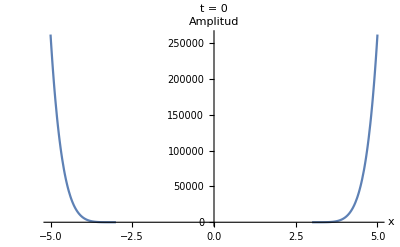

```mathematica
a=1;
b=3;
c=3;
w=1;
h=1;
m[x_]:=b*c/((b+x)*(c-x))
f[x_,a_]:=Exp[-x^2*(1-a)];
g=Integrate[x*m[x]/f[x,a],x];
Psi0[x_,t_]:=Exp[-(w/h )*g]*Exp[-I*h*w*1/2*t/h];
Plot[Psi0[x,0],{x,-5,5},PlotRange->All,AxesLabel->{"x","Amplitud"},PlotLabel->"t = 0"]
Manipulate[Plot[Abs[Psi0[x,t]],{x,-5,5},PlotRange->All,AxesLabel->{"x","Amplitud"},PlotLabel->"t = "<>ToString[t]],{t,0,10,0.1}]

Plot3D[Abs[Psi0[x,t]],{x,-5,5},{t,0,10},PlotRange->{All,All,All},AxesLabel->{"x","Tiempo","Amplitud"},PlotLabel->"Evolución Temporal",BoxRatios->{1,1,1}]
```